```mathematica
ClearGlobal[]:=(ClearAll["Global`*"];Clear[Derivative];);
```

```mathematica
ClearGlobal[]
```

```mathematica
RemoveGlobal[]:=(ClearGlobal[];Remove["Global`*"];);
```

```mathematica
RemoveGlobal[]
```

# Good genes for daughters

Reproducing Seger-Trivers (1986) paper “Asymmetry in the evolution of female mating preferences”

## Intro

```mathematica
table:= {{"", "T_1","T_2"}, {"Males", "α_1", "α_2"} , {"Females", "β_1", "β_2"}}
```

```mathematica
Grid[table,ItemStyle->{FontFamily->"Latin Modern Roman"},Spacings->{2,.75}, Alignment->Right,Dividers->{{2->True},{2->True}}]
```

| T_1 | T_2
Males | α_1 | α_2
Females | β_1 | β_2

## Basic Model

### Basic definitions

```mathematica
Subscript[W, 2] := Subscript[t', 2] / Subscript[t, 2]
```

```mathematica
Subscript[W, 1] := Subscript[t', 1] / Subscript[t, 1]
```

### Frequencies after selection

```mathematica
Subscript[Superscript[t, m], 1] = Subscript[α, 1] Subscript[t, 1] / (Subscript[α, 1] Subscript[t, 1] +Subscript[α, 2] Subscript[t, 2] )
```

(t_1 α_1)/(t_1 α_1+t_2 α_2)

```mathematica
Subscript[Superscript[t, m], 2] = Simplify[1- Subscript[Superscript[t, m], 1]]
```

(t_2 α_2)/(t_1 α_1+t_2 α_2)

```mathematica
Subscript[Superscript[t, f], 1] = Subscript[β, 1] Subscript[t, 1] / (Subscript[β, 1] Subscript[t, 1] +Subscript[β, 2] Subscript[t, 2] )
```

(t_1 β_1)/(t_1 β_1+t_2 β_2)

```mathematica
Subscript[Superscript[t, f], 2] = Simplify[1- Subscript[Superscript[t, f], 1]]
```

(t_2 β_2)/(t_1 β_1+t_2 β_2)

### Calculating reproductive success

Reproductive success of T_2 allele(labeled V_2 in the paper):

t'_2=1/2(U_12 p_1+U_22 p_2+(t^f)_2)

Same for T_1 allele (labeled V_1 in the paper):

t'_1=1/2(U_11 p_1+U_21 p_2+(t^f)_1)

Typing this using Superscript[] notation to avoid superscript being interpreted as power:

```mathematica
Subscript[t', 2]:=1/2(Subscript[U, 12]Subscript[p, 1] + Subscript[U, 22]Subscript[p, 2]+Subscript[Superscript[t, f],2])
```

```mathematica
Subscript[t', 1]:=1/2(Subscript[U, 11]Subscript[p, 1] + Subscript[U, 21]Subscript[p, 2]+Subscript[Superscript[t, f],1])
```

## Fixed relative preference

### Prepare for plotting

#### Female choice

```mathematica
Subscript[U, 22] = Simplify[Subscript[a, 2]*Subscript[Superscript[t, m], 2]/(Subscript[Superscript[t, m], 1]+Subscript[a, 2]*Subscript[Superscript[t, m], 2])]
```

(a_2 t_2 α_2)/(t_1 α_1+a_2 t_2 α_2)

```mathematica
Subscript[U, 11] = Simplify[Subscript[a, 1]*Subscript[Superscript[t, m], 1]/(Subscript[Superscript[t, m], 2]+Subscript[a, 1]*Subscript[Superscript[t, m], 1])]
```

(a_1 t_1 α_1)/(a_1 t_1 α_1+t_2 α_2)

```mathematica
Subscript[U, 21] := 1-Subscript[U, 22]
```

```mathematica
Subscript[U, 12] := 1-Subscript[U, 11]
```

```mathematica
Subscript[t, 1] := 1 - Subscript[t, 2]
```

```mathematica
Subscript[p, 1] := 1- Subscript[p, 2]
```

#### Plotting stuff

```mathematica
sol1= FullSimplify[Solve[Subscript[W, 1]==Subscript[W, 2], Subscript[p, 2]]]
```

{{p_2→((-(-1+t_2) α_1+a_2 t_2 α_2) (a_1 α_1 (2 (-1+t_2) β_1+(1-2 t_2) β_2)+α_2 ((1-2 t_2) β_1+2 t_2 β_2)))/((-1+a_1 a_2) α_1 α_2 ((-1+t_2) β_1-t_2 β_2))}}

```mathematica
axisFlip=#/.{x_Line|x_GraphicsComplex:>MapAt[#~Reverse~2&,x,1],x:(PlotRange->_):>x~Reverse~2}&;
```

### Impact of Selection on Asymmetry

```mathematica
pref = 3;
```

#### Fixation of T_2 allele under asymmetric preference

T_2 males are penalized only (blue line, left pane)

```mathematica
f1a1[s_] :=1-(Subscript[p,2]/.sol1 /.{Subscript[t, 2]->1} /.{Subscript[α, 1]->1,Subscript[α, 2]->1-s,Subscript[β, 1]->1,Subscript[β, 2]->1,Subscript[a, 1]->1,Subscript[a, 2]->pref})[[1]]
```

T_2 females are penalized only (orange line, left pane)

```mathematica
f1b1[s_] :=1-(Subscript[p,2]/.sol1 /.{Subscript[t, 2]->1} /.{Subscript[α, 1]->1,Subscript[α, 2]->1,Subscript[β, 1]->1,Subscript[β, 2]->1-s,Subscript[a, 1]->1,Subscript[a, 2]->pref})[[1]]
```

```mathematica
figxa := Plot[{f1a1[s],f1b1[s]}, {s, 0, 1}, PlotRange->{0,1},Frame->True,LabelStyle->Black,BaseStyle->{FontSize->12}, FrameLabel->{"s_2", "ϕ_2"},Epilog->Inset[Style["T_2",12],{1,.95},{1,1}]]
```

#### Fixation of T_1 allele under asymmetric preference

T_2 males are penalized only (blue line, left pane)

```mathematica
f1a11[s_] :=(Subscript[p,2]/.sol1 /.{Subscript[t, 2]->0} /.{Subscript[α, 1]->1,Subscript[α, 2]->1-s,Subscript[β, 1]->1,Subscript[β, 2]->1,Subscript[a, 1]->1,Subscript[a, 2]->pref})[[1]]
```

T_2 females are penalized only (orange line, left pane)

```mathematica
f1b11[s_] :=(Subscript[p,2]/.sol1 /.{Subscript[t, 2]->0} /.{Subscript[α, 1]->1,Subscript[α, 2]->1,Subscript[β, 1]->1,Subscript[β, 2]->1-s,Subscript[a, 1]->1,Subscript[a, 2]->pref})[[1]]
```

```mathematica
figxa1 := Plot[{f1a11[s],f1b11[s]}, {s, 0, 1}, PlotRange->{0,1},Frame->True,LabelStyle->Black,BaseStyle->{FontSize->12}, FrameLabel->{"s_2", "ϕ_1"},Epilog->Inset[Style["T_1",12],{1,.95},{1,1}]]
```

#### Fixation of T_2 allele under symmetric preference

T_2 males and T_1 females have the same survival penalty (blue line, right pane)

```mathematica
f1a2s[s_] :=1-(Subscript[p,2]/.sol1 /.{Subscript[t, 2]->1} /.{Subscript[α, 1]->1,Subscript[α, 2]->1-s,Subscript[β, 1]->1-s,Subscript[β, 2]->1,Subscript[a, 1]->1,Subscript[a, 2]->pref})[[1]]
```

T_1 males and T_2 females have the same survival penalty (orange line, right pane)

```mathematica
f1b2s[s_] :=1-(Subscript[p,2]/.sol1 /.{Subscript[t, 2]->1} /.{Subscript[α, 1]->1-s,Subscript[α, 2]->1,Subscript[β, 1]->1,Subscript[β, 2]->1-s,Subscript[a, 1]->1,Subscript[a, 2]->pref})[[1]]
```

```mathematica
figxbs := Plot[{f1a2s[s],f1b2s[s]}, {s, 0, 1}, PlotRange->{0,1},Frame->True,LabelStyle->Black,BaseStyle->{FontSize->12}, FrameLabel->{"s_12", "ϕ_2"},Epilog->{Arrowheads[{-.05,.05}],Arrow[{{0.4,0.38},{0.4,0.75}}],Inset[Style["T_2",12],{1,.95},{1,1}]}]
```

#### Fixation of T_1 allele under symmetric preference

T_2 males and T_1 females have the same survival penalty (blue line, left pane)

```mathematica
f1a21s[s_] :=(Subscript[p,2]/.sol1 /.{Subscript[t, 2]->0} /.{Subscript[α, 1]->1,Subscript[α, 2]->1-s,Subscript[β, 1]->1-s,Subscript[β, 2]->1,Subscript[a, 1]->pref,Subscript[a, 2]->1})[[1]]
```

T_1 males and T_2 females have the same survival penalty (orange line, left pane)

```mathematica
f1b21s[s_] :=(Subscript[p,2]/.sol1 /.{Subscript[t, 2]->0} /.{Subscript[α, 1]->1-s,Subscript[α, 2]->1,Subscript[β, 1]->1,Subscript[β, 2]->1-s,Subscript[a, 1]->pref,Subscript[a, 2]->1})[[1]]
```

```mathematica
figxb1s := Plot[{f1a21s[s],f1b21s[s]}, {s, 0, 1}, PlotRange->{0,1},Frame->True,LabelStyle->Black,BaseStyle->{FontSize->12}, FrameLabel->{"s_12", "ϕ_1"},Epilog->{Arrowheads[{-.05,.05}],Arrow[{{0.4,0.38},{0.4,0.75}}],Inset[Style["T_1",12],{1,.95},{1,1}]}]
```

#### Fixation plots

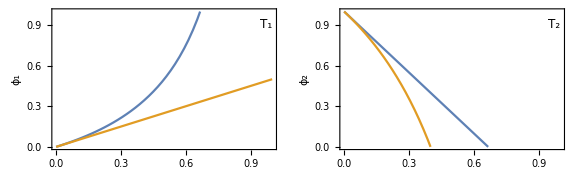

```mathematica
GraphicsRow[{figxa1,figxa},ImageSize->Large,Spacings->0]
```

Between s=0.40 and s=0.67, there is distinct asymmetry: penalizing T_2 males still allows us to fixate the harmful T_2 allele, while penalizing T_2 females cannot result in its fixation (right pane). One would think this should be compensated by the fact that penalizing T_2 males also increases chance of fixation of the benign T_1 allele compared to when T_2 females are penalized (left pane). However, when T_1 allele is fixated, no sex suffers a survival penalty, while when T_2 allele is fixated, the male sex has decreased viability.

### Impact of Preference on Asymmetry

```mathematica
sel = 0.4;
```

#### Fixation of T_2 allele under asymmetric preference

T_2 males are penalized only (blue line, left pane)

```mathematica
yf1a1[k_] :=1-(Subscript[p,2]/.sol1 /.{Subscript[t, 2]->1} /.{Subscript[α, 1]->1,Subscript[α, 2]->1-sel,Subscript[β, 1]->1,Subscript[β, 2]->1,Subscript[a, 1]->1,Subscript[a, 2]->k})[[1]]
```

T_2 females are penalized only (orange line, left pane)

```mathematica
yf1b1[k_] :=1-(Subscript[p,2]/.sol1 /.{Subscript[t, 2]->1} /.{Subscript[α, 1]->1,Subscript[α, 2]->1,Subscript[β, 1]->1,Subscript[β, 2]->1-sel,Subscript[a, 1]->1,Subscript[a, 2]->k})[[1]]
```

```mathematica
yfigxa := Plot[{yf1a1[k],yf1b1[k]}, {k, 1, 4}, PlotRange->{0,1},Frame->True,LabelStyle->Black,BaseStyle->{FontSize->12}, FrameLabel->{"a_2", "ϕ_2"},Epilog->Inset[Style["T_2",12],{4,.95},{1,1}]]
```

#### Fixation of T_1 allele under asymmetric preference

T_2 males are penalized only (blue line, left pane)

```mathematica
yf1a11[k_] :=(Subscript[p,2]/.sol1 /.{Subscript[t, 2]->0} /.{Subscript[α, 1]->1,Subscript[α, 2]->1-sel,Subscript[β, 1]->1,Subscript[β, 2]->1,Subscript[a, 1]->1,Subscript[a, 2]->k})[[1]]
```

T_2 females are penalized only (orange line, left pane)

```mathematica
yf1b11[k_] :=(Subscript[p,2]/.sol1 /.{Subscript[t, 2]->0} /.{Subscript[α, 1]->1,Subscript[α, 2]->1,Subscript[β, 1]->1,Subscript[β, 2]->1-sel,Subscript[a, 1]->1,Subscript[a, 2]->k})[[1]]
```

```mathematica
yfigxa1 := Plot[{yf1a11[k],yf1b11[k]}, {k, 1, 4}, PlotRange->{0,1},Frame->True,LabelStyle->Black,BaseStyle->{FontSize->12}, FrameLabel->{"a_2", "ϕ_1"},Epilog->Inset[Style["T_1",12],{4,.95},{1,1}]]
```

#### Fixation of T_2 allele under symmetric preference

T_2 males and T_1 females have the same survival penalty (blue line, right pane)

```mathematica
yf1a2s[k_] :=1-(Subscript[p,2]/.sol1 /.{Subscript[t, 2]->1} /.{Subscript[α, 1]->1,Subscript[α, 2]->1-sel,Subscript[β, 1]->1-sel,Subscript[β, 2]->1,Subscript[a, 1]->1,Subscript[a, 2]->k})[[1]]
```

T_1 males and T_2 females have the same survival penalty (orange line, right pane)

```mathematica
yf1b2s[k_] :=1-(Subscript[p,2]/.sol1 /.{Subscript[t, 2]->1} /.{Subscript[α, 1]->1-sel,Subscript[α, 2]->1,Subscript[β, 1]->1,Subscript[β, 2]->1-sel,Subscript[a, 1]->1,Subscript[a, 2]->k})[[1]]
```

```mathematica
yfigxbs := Plot[{yf1a2s[k],yf1b2s[k]}, {k, 1, 4}, PlotRange->{0,1},Frame->True,LabelStyle->Black,BaseStyle->{FontSize->12}, FrameLabel->{"a_2", "ϕ_2"},Epilog->{Arrowheads[{-.05,.05}],Arrow[{{2,0.12},{2,0.67}}],Inset[Style["T_2",12],{4,.95},{1,1}]}]
```

#### Fixation of T_1 allele under symmetric preference

T_2 males and T_1 females have the same survival penalty (blue line, left pane)

```mathematica
yf1a21s[k_] :=(Subscript[p,2]/.sol1 /.{Subscript[t, 2]->0} /.{Subscript[α, 1]->1,Subscript[α, 2]->1-sel,Subscript[β, 1]->1-sel,Subscript[β, 2]->1,Subscript[a, 1]->k,Subscript[a, 2]->1})[[1]]
```

T_1 males and T_2 females have the same survival penalty (orange line, left pane)

```mathematica
yf1b21s[k_] :=(Subscript[p,2]/.sol1 /.{Subscript[t, 2]->0} /.{Subscript[α, 1]->1-sel,Subscript[α, 2]->1,Subscript[β, 1]->1,Subscript[β, 2]->1-sel,Subscript[a, 1]->k,Subscript[a, 2]->1})[[1]]
```

```mathematica
yfigxb1s := Plot[{yf1a21s[k],yf1b21s[k]}, {k, 1,4}, PlotRange->{0,1},Frame->True,LabelStyle->Black,BaseStyle->{FontSize->12}, FrameLabel->{"a_1", "ϕ_1"},Epilog->{Arrowheads[{-.05,.05}],Arrow[{{2,0.12},{2,0.67}}],Inset[Style["T_1",12],{4,.95},{1,1}]}]
```

#### Fixation plots

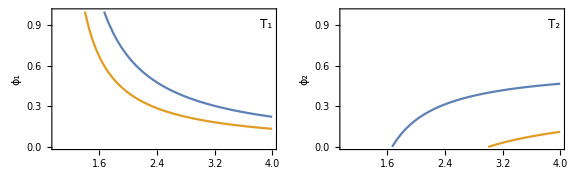

```mathematica
GraphicsRow[{yfigxa1,yfigxa},ImageSize->Large,Spacings->0]
```

### Contour plot formula

```mathematica
contourDensityPlot[f_,rx_,ry_,opts:OptionsPattern[]]:=(* //Created by Jens U.Nöckel for Mathematica 8,revised 12/2011*)Module[{img,cont,pL,p,plotRangeRule,densityOptions,contourOptions,frameOptions,rangeCoords},densityOptions=Join[FilterRules[{opts},FilterRules[Options[DensityPlot],Except[{ImageSize,Prolog,Epilog,FrameTicks,PlotLabel,ImagePadding,GridLines,Mesh,AspectRatio,PlotRangePadding,Frame,Axes}]]],{PlotRangePadding->None,ImagePadding->None,Frame->None,Axes->None}];
pL=DensityPlot[f,rx,ry,Evaluate@Apply[Sequence,densityOptions]];
p=First@Cases[{pL},Graphics[__],∞];
plotRangeRule=FilterRules[Quiet@AbsoluteOptions[p],PlotRange];
contourOptions=Join[FilterRules[{opts},FilterRules[Options[ContourPlot],Except[{Prolog,Epilog,FrameTicks,Background,ContourShading,Frame,Axes}]]],{Frame->None,Axes->None,ContourShading->False}];
(* //The density plot img and contour plot cont are created here:*)img=Rasterize[p,"Image"];
cont=If[MemberQ[{0,None},(Contours/.FilterRules[{opts},Contours])],{},ContourPlot[f,rx,ry,Evaluate@Apply[Sequence,contourOptions]]];
(* //Before showing the plots,set the PlotRange for the frame which will be drawn separately:*)frameOptions=Join[FilterRules[{opts},FilterRules[Options[Graphics],Except[{PlotRangeClipping,PlotRange}]]],{plotRangeRule,Frame->True,PlotRangeClipping->True}];
rangeCoords=Transpose[PlotRange/.plotRangeRule];
(* //To align the image img with the contour plot,enclose img in a bounding box rectangle of the same dimensions as cont,
//and then combine with cont using Show:*)If[Head[pL]===Legended,Legended[#,pL[[2]]],#]&@Show[Graphics[{Inset[Show[SetAlphaChannel[img,"ShadingOpacity"/.{opts}/.{"ShadingOpacity"->1}],AspectRatio->Full],rangeCoords[[1]],{0,0},rangeCoords[[2]]-rangeCoords[[1]]]},PlotRangePadding->None],cont,Evaluate@Apply[Sequence,frameOptions]]]
```

### Contour plots

#### Figure 1

```mathematica
args1M = {Subscript[α, 1] -> 1, Subscript[α, 2] -> 0.6,Subscript[β, 1] -> 1, Subscript[β, 2] -> 1, Subscript[a, 1] -> 1, Subscript[a, 2]->3};
```

```mathematica
args1F = {Subscript[α, 1] -> 1, Subscript[α, 2] -> 1,Subscript[β, 1] -> 1, Subscript[β, 2] -> 0.6, Subscript[a, 1] -> 1, Subscript[a, 2]->3};
```

```mathematica
fig1Meq =Plot[Evaluate[Subscript[p,2]/.sol1 /. args1M], {Subscript[t, 2], 0, 1}, PlotRange->{0,1},PlotStyle->Black, AspectRatio->1, FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]}, Frame->True,BaseStyle->{FontSize->12}] //axisFlip;
```

```mathematica
fig1Feq =Plot[Evaluate[Subscript[p,2]/.sol1 /. args1F], {Subscript[t, 2], 0, 1},PlotStyle->Black, PlotRange->{0,1}, Frame->True, LabelStyle->Black,AspectRatio->1, FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]},BaseStyle->{FontSize->12}] // axisFlip;
```

```mathematica
fig1M := contourDensityPlot[Log[Subscript[W, 2]/Subscript[W, 1]] /.args1M,{Subscript[p, 2],0,1},{Subscript[t, 2],0,1},  ColorFunction->(ColorData["ThermometerColors"][#1 + 0.5]&),ColorFunctionScaling->False, LabelStyle->Black,ContourStyle->Directive[Black, Dashed],FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]},BaseStyle->{FontSize->12},Epilog->Inset[Style["♂",16],{.075,.925},{0,0}]]
```

```mathematica
fig1F := contourDensityPlot[Log[Subscript[W, 2]/Subscript[W, 1]] /. args1F,{Subscript[p, 2],0,1},{Subscript[t, 2],0,1}, ColorFunction->(ColorData["ThermometerColors"][#1 + 0.5]&),ColorFunctionScaling->False, LabelStyle->Black,ContourStyle->Directive[Black, Dashed],FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]},BaseStyle->{FontSize->12},Epilog->Inset[Style["♀",16],{.075,.925},{0,0}]]
```

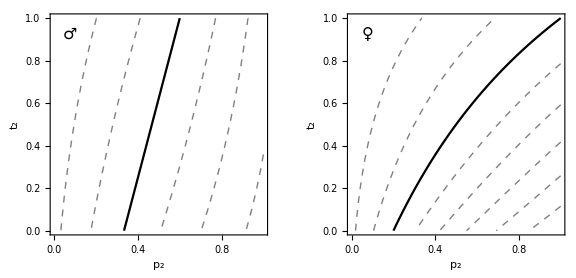

```mathematica
GraphicsRow[{Show[fig1M, fig1Meq], Show[fig1F, fig1Feq]}, ImageSize->Large]
```

#### Figure 2

```mathematica
args2a = {Subscript[α, 1] -> 1, Subscript[α, 2] -> 0.8,Subscript[β, 1] -> 0.8, Subscript[β, 2] -> 1, Subscript[a, 1] ->1.05, Subscript[a, 2]->1.05};
```

```mathematica
fig2aeq = Plot[Evaluate[Subscript[p,2]/.sol1 /. args2a], {Subscript[t, 2], 0, 1}, PlotRange->{0,1},PlotStyle->Black, Frame->True, LabelStyle->Black,FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]},BaseStyle->{FontSize->12}]//axisFlip;
```

```mathematica
fig2a:= contourDensityPlot[Log[Subscript[W, 2]/Subscript[W, 1]] /.args2a,{Subscript[p, 2],0,1},{Subscript[t, 2],0,1},  ColorFunction->(ColorData["ThermometerColors"][#1 + 0.5]&),ColorFunctionScaling->False, LabelStyle->Black,ContourStyle->Directive[Black, Dashed],FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]},BaseStyle->{FontSize->12}]
```

```mathematica
args2b = {Subscript[α, 1] ->0.8, Subscript[α, 2] -> 1,Subscript[β, 1] -> 1, Subscript[β, 2] -> 0.8, Subscript[a, 1] ->1.05, Subscript[a, 2]->1.05};
```

```mathematica
fig2beq = Plot[Evaluate[Subscript[p,2]/.sol1 /. args2b], {Subscript[t, 2], 0, 1}, PlotRange->{0,1},PlotStyle->Black, Frame->True, LabelStyle->Black,FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]},BaseStyle->{FontSize->12}]//axisFlip;
```

```mathematica
fig2b:= contourDensityPlot[Log[Subscript[W, 2]/Subscript[W, 1]] /.args2b,{Subscript[p, 2],0,1},{Subscript[t, 2],0,1},  ColorFunction->(ColorData["ThermometerColors"][#1 + 0.5]&),ColorFunctionScaling->False, LabelStyle->Black,ContourStyle->Directive[Black, Dashed],FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]},BaseStyle->{FontSize->12}]
```

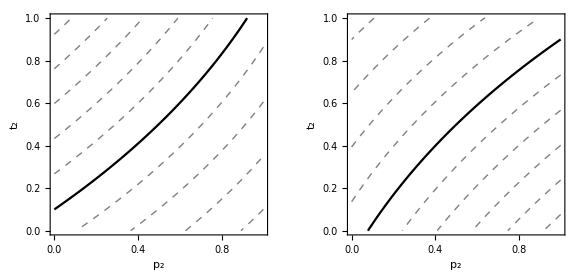

```mathematica
GraphicsRow[{Show[fig2a, fig2aeq], Show[fig2b, fig2beq]}, ImageSize->Large]
```

slight favor towards T_2

## Best-of-2

### Female choice

```mathematica
Subscript[U, 22] = Subscript[Superscript[t,m], 2] + Subscript[c,2] *Subscript[Superscript[t,m], 1]*Subscript[Superscript[t,m], 2]
```

(c_2 (1-t_2) t_2 α_1 α_2)/((1-t_2) α_1+t_2 α_2)^2+(t_2 α_2)/((1-t_2) α_1+t_2 α_2)

```mathematica
Subscript[U, 11] = Subscript[Superscript[t,m], 1] + Subscript[c,1] *Subscript[Superscript[t,m], 1]*Subscript[Superscript[t,m], 2]
```

(c_1 (1-t_2) t_2 α_1 α_2)/((1-t_2) α_1+t_2 α_2)^2+((1-t_2) α_1)/((1-t_2) α_1+t_2 α_2)

### Best-of-2 Plots

```mathematica
sol2= FullSimplify[Solve[Subscript[W, 1]==Subscript[W, 2], Subscript[p, 2]]]
```

{{p_2→(-(-1+t_2) α_1^2 (2 (-1+t_2) β_1+(1-2 t_2) β_2)+t_2 α_2^2 ((1-2 t_2) β_1+2 t_2 β_2)+α_1 α_2 ((-1+t_2) (-1+c_1+4 t_2) β_1-t_2 (-3+c_1+4 t_2) β_2))/((c_1+c_2) α_1 α_2 ((-1+t_2) β_1-t_2 β_2))}}

```mathematica
args3M := {Subscript[α, 1] -> 1, Subscript[α, 2] -> 0.6,Subscript[β, 1] -> 1, Subscript[β, 2] -> 1, Subscript[c, 1] -> 0, Subscript[c, 2]->1}
```

```mathematica
args3F := {Subscript[α, 1] -> 1, Subscript[α, 2] ->1,Subscript[β, 1] -> 1, Subscript[β, 2] -> 0.6, Subscript[c, 1] -> 0, Subscript[c, 2]->1}
```

```mathematica
fig3Meq :=Plot[Evaluate[Subscript[p,2]/.sol2 /. args3M], {Subscript[t, 2], 0, 1}, PlotRange->{0,1},PlotStyle->Black, AspectRatio->1, FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]}, Frame->True,BaseStyle->{FontSize->12}]//axisFlip
```

```mathematica
fig3M := contourDensityPlot[Log[Subscript[W, 2]/Subscript[W, 1]] /.args3M,{Subscript[p, 2],0,1},{Subscript[t, 2],0,1},  ColorFunction->(ColorData["ThermometerColors"][#1 + 0.5]&),ColorFunctionScaling->False, LabelStyle->Black,ContourStyle->Directive[Black, Dashed],FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]},BaseStyle->{FontSize->12},Epilog->Inset[Style["♂",16],{.075,.925},{0,0}]]
```

```mathematica
fig3Feq :=Plot[Evaluate[Subscript[p,2]/.sol2 /. args3F], {Subscript[t, 2], 0, 1}, PlotRange->{0,1},PlotStyle->Black, AspectRatio->1, FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]}, Frame->True,BaseStyle->{FontSize->12}]//axisFlip
```

```mathematica
fig3F:= contourDensityPlot[Log[Subscript[W, 2]/Subscript[W, 1]] /.args3F,{Subscript[p, 2],0,1},{Subscript[t, 2],0,1},  ColorFunction->(ColorData["ThermometerColors"][#1 + 0.5]&),ColorFunctionScaling->False, LabelStyle->Black,ContourStyle->Directive[Black, Dashed],FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]},BaseStyle->{FontSize->12},Epilog->Inset[Style["♀",16],{.075,.925},{0,0}]]
```

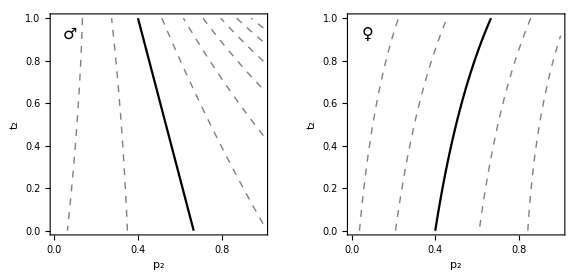

```mathematica
GraphicsRow[{Show[fig3M, fig3Meq], Show[fig3F, fig3Feq]}, ImageSize->Large]
```

### Impact of selection on asymmetry

```mathematica
prefN = 1;
```

#### Fixation of T_2 allele under asymmetric preference

T_2 males are penalized only (blue line, left pane)

```mathematica
g1a1[s_] :=1-(Subscript[p,2]/.sol2 /.{Subscript[t, 2]->1} /.{Subscript[α, 1]->1,Subscript[α, 2]->1-s,Subscript[β, 1]->1,Subscript[β, 2]->1,Subscript[c, 1]->0,Subscript[c, 2]->prefN})[[1]]
```

T_2 females are penalized only (orange line, left pane)

```mathematica
g1b1[s_] :=1-(Subscript[p,2]/.sol2 /.{Subscript[t, 2]->1} /.{Subscript[α, 1]->1,Subscript[α, 2]->1,Subscript[β, 1]->1,Subscript[β, 2]->1-s,Subscript[c, 1]->0,Subscript[c, 2]->prefN})[[1]]
```

```mathematica
gigxa := Plot[{g1a1[s],g1b1[s]}, {s, 0, 1}, PlotRange->{0,1},Frame->True,LabelStyle->Black,BaseStyle->{FontSize->12}, FrameLabel->{"s_2", "ϕ_2"},Epilog->Inset[Style["T_2",12],{1,.95},{1,1}]]
```

#### Fixation of T_1 allele under asymmetric preference

T_2 males are penalized only (blue line, left pane)

```mathematica
g1a11[s_] :=(Subscript[p,2]/.sol2 /.{Subscript[t, 2]->0} /.{Subscript[α, 1]->1,Subscript[α, 2]->1-s,Subscript[β, 1]->1,Subscript[β, 2]->1,Subscript[c, 1]->0,Subscript[c, 2]->prefN})[[1]]
```

T_2 females are penalized only (orange line, left pane)

```mathematica
g1b11[s_] :=(Subscript[p,2]/.sol2 /.{Subscript[t, 2]->0} /.{Subscript[α, 1]->1,Subscript[α, 2]->1,Subscript[β, 1]->1,Subscript[β, 2]->1-s,Subscript[c, 1]->0,Subscript[c, 2]->prefN})[[1]]
```

```mathematica
gigxa1 := Plot[{g1a11[s],g1b11[s]}, {s, 0, 1}, PlotRange->{0,1},Frame->True,LabelStyle->Black,BaseStyle->{FontSize->12}, FrameLabel->{"s_2", "ϕ_1"},Epilog->Inset[Style["T_1",12],{1,.95},{1,1}]]
```

#### Fixation of T_2 allele under symmetric preference

T_2 males and T_1 females have the same survival penalty (blue line, right pane)

```mathematica
g1a2s[s_] :=1-(Subscript[p,2]/.sol2 /.{Subscript[t, 2]->1} /.{Subscript[α, 1]->1,Subscript[α, 2]->1-s,Subscript[β, 1]->1-s,Subscript[β, 2]->1,Subscript[c, 1]->0,Subscript[c, 2]->prefN})[[1]]
```

T_1 males and T_2 females have the same survival penalty (orange line, right pane)

```mathematica
g1b2s[s_] :=1-(Subscript[p,2]/.sol2/.{Subscript[t, 2]->1} /.{Subscript[α, 1]->1-s,Subscript[α, 2]->1,Subscript[β, 1]->1,Subscript[β, 2]->1-s,Subscript[c, 1]->0,Subscript[c, 2]->prefN})[[1]]
```

```mathematica
gigxbs := Plot[{g1a2s[s],g1b2s[s]}, {s, 0, 1}, PlotRange->{0,1},Frame->True,LabelStyle->Black,BaseStyle->{FontSize->12}, FrameLabel->{"s_12", "ϕ_2"},Epilog->Inset[Style["T_2",12],{1,.95},{1,1}]]
```

#### Fixation of T_1 allele under symmetric preference

T_2 males and T_1 females have the same survival penalty (blue line, left pane)

```mathematica
g1a21s[s_] :=(Subscript[p,2]/.sol2 /.{Subscript[t, 2]->0} /.{Subscript[α, 1]->1,Subscript[α, 2]->1-s,Subscript[β, 1]->1-s,Subscript[β, 2]->1,Subscript[c, 1]->prefN,Subscript[c, 2]->0})[[1]]
```

T_1 males and T_2 females have the same survival penalty (orange line, left pane)

```mathematica
g1b21s[s_] :=(Subscript[p,2]/.sol2 /.{Subscript[t, 2]->0} /.{Subscript[α, 1]->1-s,Subscript[α, 2]->1,Subscript[β, 1]->1,Subscript[β, 2]->1-s,Subscript[c, 1]->prefN,Subscript[c, 2]->0})[[1]]
```

```mathematica
gigxb1s := Plot[{g1a21s[s],g1b21s[s]}, {s, 0, 1}, PlotRange->{0,1},Frame->True,LabelStyle->Black,BaseStyle->{FontSize->12}, FrameLabel->{"s_12", "ϕ_1"},Epilog->Inset[Style["T_1",12],{1,0.95},{1,1}]]
```

#### Fixation plots

Switching to best-of-2 model results in an increase of the area where the discrepancy described above exists:

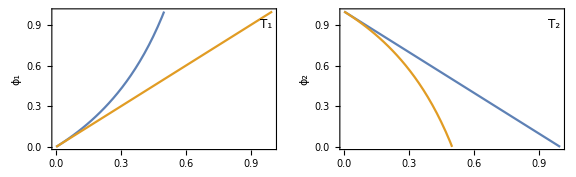

```mathematica
GraphicsRow[{gigxa1,gigxa},ImageSize->Large,Spacings->0]
```

In order to see the asymmetry more clearly, it helps to make the parts of the model not relevant to the analysis more symmetric. Suppose, under condition A (blue line) T_2 allele decreases the fitness of males while increasing that of females by the same amount, while under condition B (orange line), the same allele increases the fitness of males while decreasing that of females carrying it. Under symmetry, one would expect both lines to coincide. That is not, however, what happens:

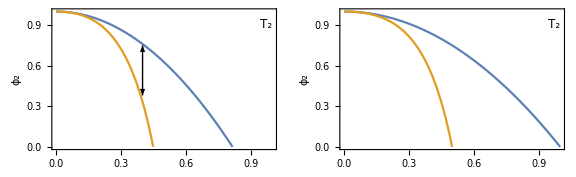

```mathematica
GraphicsRow[{figxbs,gigxbs},ImageSize->Large, Spacings->0]
```

The left pane shows chance of fixation of  T_2 allele under fixed-preference model, the right one under best-of-2 model. The blue and orange lines do not coincide, and the discrepancy is stronger under the best-of-2 model, as expected.

### Impact of preference on asymmetry

```mathematica
sel = 0.4;
```

#### Fixation of T_2 allele under asymmetric preference

T_2 males are penalized only (blue line, left pane)

```mathematica
yg1a1[k_] :=1-(Subscript[p,2]/.sol2 /.{Subscript[t, 2]->1} /.{Subscript[α, 1]->1,Subscript[α, 2]->1-sel,Subscript[β, 1]->1,Subscript[β, 2]->1,Subscript[c, 1]->0,Subscript[c, 2]->k})[[1]]
```

T_2 females are penalized only (orange line, left pane)

```mathematica
yg1b1[k_] :=1-(Subscript[p,2]/.sol2 /.{Subscript[t, 2]->1} /.{Subscript[α, 1]->1,Subscript[α, 2]->1,Subscript[β, 1]->1,Subscript[β, 2]->1-sel,Subscript[c, 1]->0,Subscript[c, 2]->k})[[1]]
```

```mathematica
ygigxa := Plot[{yg1a1[k],yg1b1[k]}, {k, 0, 1}, PlotRange->{0,1},Frame->True,LabelStyle->Black,BaseStyle->{FontSize->12}, FrameLabel->{"c_2", "ϕ_2"},Epilog->Inset[Style["T_2",12],{1,.95},{1,1}]]
```

#### Fixation of T_1 allele under asymmetric preference

T_2 males are penalized only (blue line, left pane)

```mathematica
yg1a11[k_] :=(Subscript[p,2]/.sol2 /.{Subscript[t, 2]->0} /.{Subscript[α, 1]->1,Subscript[α, 2]->1-sel,Subscript[β, 1]->1,Subscript[β, 2]->1,Subscript[c, 1]->0,Subscript[c, 2]->k})[[1]]
```

T_2 females are penalized only (orange line, left pane)

```mathematica
yg1b11[k_] :=(Subscript[p,2]/.sol2 /.{Subscript[t, 2]->0} /.{Subscript[α, 1]->1,Subscript[α, 2]->1,Subscript[β, 1]->1,Subscript[β, 2]->1-sel,Subscript[c, 1]->0,Subscript[c, 2]->k})[[1]]
```

```mathematica
ygigxa1 := Plot[{yg1a11[k],yg1b11[k]}, {k, 0, 1}, PlotRange->{0,1},Frame->True,LabelStyle->Black,BaseStyle->{FontSize->12}, FrameLabel->{"c_2", "ϕ_1"},Epilog->Inset[Style["T_1",12],{1,.95},{1,1}]]
```

#### Fixation of T_2 allele under symmetric preference

T_2 males and T_1 females have the same survival penalty (blue line, right pane)

```mathematica
yg1a2s[k_] :=1-(Subscript[p,2]/.sol2 /.{Subscript[t, 2]->1} /.{Subscript[α, 1]->1,Subscript[α, 2]->1-sel,Subscript[β, 1]->1-sel,Subscript[β, 2]->1,Subscript[c, 1]->0,Subscript[c, 2]->k})[[1]]
```

T_1 males and T_2 females have the same survival penalty (orange line, right pane)

```mathematica
yg1b2s[k_] :=1-(Subscript[p,2]/.sol2/.{Subscript[t, 2]->1} /.{Subscript[α, 1]->1-sel,Subscript[α, 2]->1,Subscript[β, 1]->1,Subscript[β, 2]->1-sel,Subscript[c, 1]->0,Subscript[c, 2]->k})[[1]]
```

```mathematica
ygigxbs := Plot[{yg1a2s[k],yg1b2s[k]}, {k, 0, 1}, PlotRange->{0,1},Frame->True,LabelStyle->Black,BaseStyle->{FontSize->12}, FrameLabel->{"c_2", "ϕ_2"},Epilog->Inset[Style["T_2",12],{1,.95},{1,1}]]
```

#### Fixation of T_1 allele under symmetric preference

T_2 males and T_1 females have the same survival penalty (blue line, left pane)

```mathematica
yg1a21s[k_] :=(Subscript[p,2]/.sol2 /.{Subscript[t, 2]->0} /.{Subscript[α, 1]->1,Subscript[α, 2]->1-sel,Subscript[β, 1]->1-sel,Subscript[β, 2]->1,Subscript[c, 1]->k,Subscript[c, 2]->0})[[1]]
```

T_1 males and T_2 females have the same survival penalty (orange line, left pane)

```mathematica
yg1b21s[k_] :=(Subscript[p,2]/.sol2 /.{Subscript[t, 2]->0} /.{Subscript[α, 1]->1-sel,Subscript[α, 2]->1,Subscript[β, 1]->1,Subscript[β, 2]->1-sel,Subscript[c, 1]->k,Subscript[c, 2]->0})[[1]]
```

```mathematica
ygigxb1s := Plot[{yg1a21s[k],yg1b21s[k]}, {k, 0, 1}, PlotRange->{0,1},Frame->True,LabelStyle->Black,BaseStyle->{FontSize->12}, FrameLabel->{"c_1", "ϕ_1"},Epilog->Inset[Style["T_1",12],{1,.95},{1,1}]]
```

#### Fixation plots

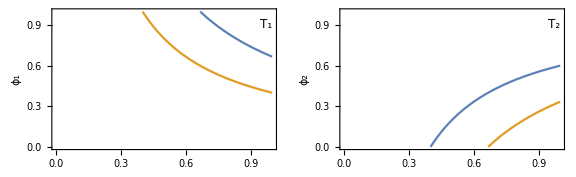

```mathematica
GraphicsRow[{ygigxa1,ygigxa},ImageSize->Large,Spacings->0]
```

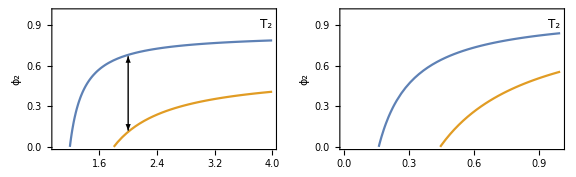

```mathematica
GraphicsRow[{yfigxbs,ygigxbs},ImageSize->Large, Spacings->0]
```

### Best-of-2 Plots (Super-Asymmetry)

```mathematica
sol2= FullSimplify[Solve[Subscript[W, 1]==Subscript[W, 2], Subscript[p, 2]]]
```

{{p_2→(-(-1+t_2) α_1^2 (2 (-1+t_2) β_1+(1-2 t_2) β_2)+t_2 α_2^2 ((1-2 t_2) β_1+2 t_2 β_2)+α_1 α_2 ((-1+t_2) (-1+c_1+4 t_2) β_1-t_2 (-3+c_1+4 t_2) β_2))/((c_1+c_2) α_1 α_2 ((-1+t_2) β_1-t_2 β_2))}}

```mathematica
args3M := {Subscript[α, 1] -> 1, Subscript[α, 2] -> 0.6,Subscript[β, 1] -> 0.6, Subscript[β, 2] ->  1, Subscript[c, 1] -> 0, Subscript[c, 2]->0.4}
```

```mathematica
args3F := {Subscript[α, 1] ->0.6, Subscript[α, 2] ->1,Subscript[β, 1] -> 1, Subscript[β, 2] -> 0.6, Subscript[c, 1] -> 0, Subscript[c, 2]->0.4}
```

```mathematica
fig3Meq :=Plot[Evaluate[Subscript[p,2]/.sol2 /. args3M], {Subscript[t, 2], 0, 1}, PlotRange->{0,1},PlotStyle->Black, AspectRatio->1, FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]}, Frame->True,BaseStyle->{FontSize->12}]//axisFlip
```

```mathematica
fig3M := contourDensityPlot[Log[Subscript[W, 2]/Subscript[W, 1]] /.args3M,{Subscript[p, 2],0,1},{Subscript[t, 2],0,1},  ColorFunction->(ColorData["ThermometerColors"][#1 + 0.5]&),ColorFunctionScaling->False, LabelStyle->Black,ContourStyle->Directive[Black, Dashed],FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]},BaseStyle->{FontSize->12},Epilog->Inset[Style["♂",16],{.075,.925},{0,0}]]
```

```mathematica
fig3Feq :=Plot[Evaluate[Subscript[p,2]/.sol2 /. args3F], {Subscript[t, 2], 0, 1}, PlotRange->{0,1},PlotStyle->Black, AspectRatio->1, FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]}, Frame->True,BaseStyle->{FontSize->12}]//axisFlip
```

```mathematica
fig3F:= contourDensityPlot[Log[Subscript[W, 2]/Subscript[W, 1]] /.args3F,{Subscript[p, 2],0,1},{Subscript[t, 2],0,1},  ColorFunction->(ColorData["ThermometerColors"][#1 + 0.5]&),ColorFunctionScaling->False, LabelStyle->Black,ContourStyle->Directive[Black, Dashed],FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]},BaseStyle->{FontSize->12},Epilog->Inset[Style["♀",16],{.075,.925},{0,0}]]
```

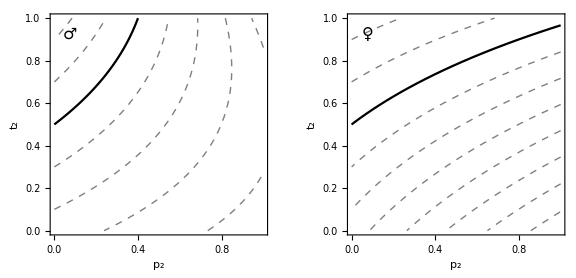

```mathematica
GraphicsRow[{Show[fig3M, fig3Meq], Show[fig3F, fig3Feq]}, ImageSize->Large]
```

## Best-of-N

### Female choice

```mathematica
Subscript[U, 22] = 1-Subscript[Superscript[t,m], 1]^n
```

1-(((1-t_2) α_1)/((1-t_2) α_1+t_2 α_2))^n

```mathematica
Subscript[U, 11] = Subscript[Superscript[t,m], 1]
```

((1-t_2) α_1)/((1-t_2) α_1+t_2 α_2)

### Plots

```mathematica
sol3= FullSimplify[Solve[Subscript[W, 1]==Subscript[W, 2], Subscript[p, 2]]]
```

{{p_2→-((-1+t_2) t_2 (α_1 (2 (-1+t_2) β_1+(1-2 t_2) β_2)+α_2 ((1-2 t_2) β_1+2 t_2 β_2)))/((-(-1+t_2) α_1+(-1+t_2) α_1 (((-1+t_2) α_1)/((-1+t_2) α_1-t_2 α_2))^(-1+n)) ((-1+t_2) β_1-t_2 β_2))}}

```mathematica
args4M := {Subscript[α, 1] -> 1, Subscript[α, 2] -> 0.6,Subscript[β, 1] -> 1, Subscript[β, 2] -> 1, n-> 3}
```

```mathematica
args4F := {Subscript[α, 1] -> 1, Subscript[α, 2] ->1,Subscript[β, 1] -> 1, Subscript[β, 2] -> 0.6, n-> 3}
```

```mathematica
fig4Meq :=Plot[Evaluate[Subscript[p,2]/.sol3 /. args4M], {Subscript[t, 2], 0, 1}, PlotRange->{0,1},PlotStyle->Black, AspectRatio->1, FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]}, Frame->True,BaseStyle->{FontSize->12}]//axisFlip
```

```mathematica
fig4M := contourDensityPlot[Log[Subscript[W, 2]/Subscript[W, 1]] /.args4M,{Subscript[p, 2],0,1},{Subscript[t, 2],0,1},  ColorFunction->(ColorData["ThermometerColors"][#1 + 0.5]&),ColorFunctionScaling->False, LabelStyle->Black,ContourStyle->Directive[Black, Dashed],FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]},BaseStyle->{FontSize->12},Epilog->Inset[Style["♂",16],{.075,.925},{0,0}]]
```

```mathematica
fig4Feq :=Plot[Evaluate[Subscript[p,2]/.sol3 /. args4F], {Subscript[t, 2], 0, 1}, PlotRange->{0,1},PlotStyle->Black, AspectRatio->1, FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]}, Frame->True,BaseStyle->{FontSize->12}]//axisFlip
```

```mathematica
fig4F:= contourDensityPlot[Log[Subscript[W, 2]/Subscript[W, 1]] /.args4F,{Subscript[p, 2],0,1},{Subscript[t, 2],0,1},  ColorFunction->(ColorData["ThermometerColors"][#1 + 0.5]&),ColorFunctionScaling->False, LabelStyle->Black,ContourStyle->Directive[Black, Dashed],FrameLabel->{Defer[Subscript[p, 2]], Defer[Subscript[t, 2]]},BaseStyle->{FontSize->12},Epilog->Inset[Style["♀",16],{.075,.925},{0,0}]]
```

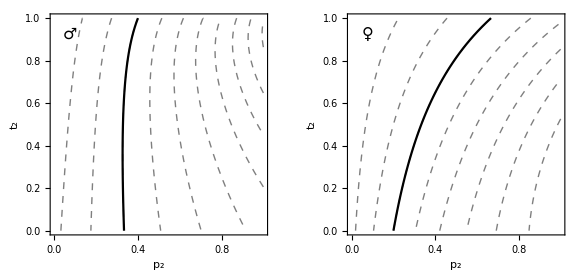

```mathematica
GraphicsRow[{Show[fig4M, fig4Meq], Show[fig4F, fig4Feq]}, ImageSize->Large]
```